```mathematica
hsdata=Import["/home/shams/Downloads/IDS/housing.csv"];
```

```mathematica
hsdata//Dataset
```

Dataset[<>]

```mathematica
hsdata2=hsdata[[2;;2000,{3,4,6,7,8,9}]];
```

```mathematica
hsdata2 //Shallow
```

{{41.,880.,322.,126.,8.3252,452600.},{21.,7099.,2401.,1138.,8.3014,358500.},{52.,1467.,496.,177.,7.2574,352100.},{52.,1274.,558.,219.,5.6431,341300.},{52.,1627.,565.,259.,3.8462,342200.},{52.,919.,413.,193.,4.0368,269700.},{52.,2535.,1094.,514.,3.6591,299200.},{52.,3104.,1157.,647.,3.12,241400.},{42.,2555.,1206.,595.,2.0804,226700.},{52.,3549.,1551.,714.,3.6912,261100.},«1989»}

```mathematica
heads=hsdata[[1,{3,4,6,7,8,9}]]
```

{housing_median_age,total_rooms,population,households,median_income,median_house_value}

```mathematica
heads=hsdata[[1,{3,4,6,7,8,9}]]
```

{housing_median_age,total_rooms,population,households,median_income,median_house_value}

```mathematica
matrixCorr=Correlation[hsdata2];
```

```mathematica
Ylabel=Transpose[{Range[1,6],heads}];
```

```mathematica
Xlabel=Transpose[{Range[1,6],heads}];
```

```mathematica
MatrixPlot[matrixCorr,ColorFunction->"ThermometerColors",PlotLegends->BarLegend[Automatic],FrameTicks->{Ylabel,Xlabel},ImageSize->Large]
```

-Graphics-

```mathematica
mydata2columns=hsdata[[2;;2000,{8,9}]];
```

```mathematica
mydata2columns=hsdata[[2;;2000,{8,9}]];
```

```mathematica
hsdata[[1;;3,{8,9}]]
```

{{median_income,median_house_value},{8.3252,452600.},{8.3014,358500.}}

```mathematica
mydata2columns //Shallow
```

{{8.3252,452600.},{8.3014,358500.},{7.2574,352100.},{5.6431,341300.},{3.8462,342200.},{4.0368,269700.},{3.6591,299200.},{3.12,241400.},{2.0804,226700.},{3.6912,261100.},«1989»}

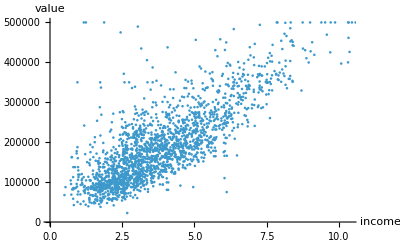

```mathematica
ListPlot[mydata2columns, AxesLabel->{"income", "value"}]
```

```mathematica
mylinearmodel=LinearModelFit[mydata2columns,x,x]
```

FittedModel[…]

```mathematica
mylinearmodel["BestFitParameters"]
```

{35314.6,40315.1}

```mathematica
mylinearmodel[12]
```

519096.

```mathematica
mylinearmodel@@{10}
```

438465.

```mathematica
titanic=ExampleData[{"Dataset","Titanic"}]
```

```mathematica
titData=Drop[GroupBy[titanic,#"survived"&],None,None,{4}]//Normal
```

```mathematica
MyModelSurvived = Classify[titData]
```

ClassifierFunction[…]

```mathematica
MyModelSurvived[{"1st",20,"male"}]
```

True

```mathematica
titanicSurvivedClean=Drop[GroupBy[titanic,#"survived"&],None,None,{4}]
```

```mathematica
Cases[titanicSurvivedClean//Normal,KeyValuePattern[{"class"->"1st","age"->20,"sex"->"male"}],2]
```

{}

```mathematica
Cases[titanic//Normal,KeyValuePattern[{"class"->"1st","age"->2,"sex"->"female"}],3]
```

{<|class→1st,age→2,sex→female,survived→False|>}

```mathematica
Count[GroupBy[titanic,"class"],#,Infinity]&/@{"1st","2nd","3rd"}
```

{323,277,709}

```mathematica
GroupBy[titanic,"class"]
```

```mathematica
databottle={"Natural mineral water","Natural Spring Water","pure drinking water","Radnor Hills Water","Premium Pure Drinking Water","Still Mountain Water from Scotland"};
```

```mathematica
Select[databottle,StringContainsQ[#]]&/@{"water","Hills"}
```

{{Natural mineral water,pure drinking water},{Radnor Hills Water}}

```mathematica
Select[databottle,StringQ]//Length
```

6

```mathematica
Cases[databottle,_String]//Length
```

6

```mathematica
Select[databottle,StringContainsQ[#]]&/@{"water"}
```

{{Natural mineral water,pure drinking water}}

```mathematica
Select[databottle,StringContainsQ[#]]&/@{"water","Hills"}
```

{{Natural mineral water,pure drinking water},{Radnor Hills Water}}

```mathematica
Select[databottle,StringContainsQ[#]]&/@{"water"}
```

{{Natural mineral water,pure drinking water}}

```mathematica
databottle[[1;;-2]]
```

{Natural mineral water,Natural Spring Water,pure drinking water,Radnor Hills Water,Premium Pure Drinking Water}

```mathematica
data1={10,20};
```

```mathematica
w={0.10,0.90}
```

{0.1,0.9}

```mathematica
pp=WeightedData[data1,w]
```

WeightedData[…]

```mathematica
Mean[pp]
```

19.

```mathematica
{1000,1001,1002}//Mean
```

1001

```mathematica
adjacency={{0,0,0,1,1},{0,0,0,1,0},{0,1,0,1,0},{1,1,1,0,1},{1,0,0,1,0}};
```

```mathematica
labels={1->"1",2->"2",3->"3",4->"4",5->"5"};
```

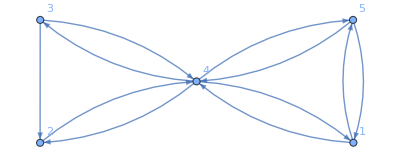

```mathematica
a=AdjacencyGraph[(adjacency),VertexLabels->"Name"]
```

```mathematica
FindGraphCommunities[a]
```

{{1,4,5},{2,3}}

```mathematica
VertexConnectivity[a]//Timing
```

{0.011366,1}

```mathematica
FindShortestPath[a,1,3]
```

{1,4,3}

```mathematica
schema=RelationalDatabase[DatabaseReference[File[FindFile["ExampleData/ecommerce-database.sqlite"]]]]
```

RelationalDatabase[…]

```mathematica
store22 = EntityStore[schema]
```

EntityStore[…]

```mathematica
EntityRegister[store22]
```

EntityRegister::shadow: Types {productlines,payments,orders,offices,customers,products,orderdetails,employees} in EntityStore[<|Types→<|«1»|>|>,RelationalDatabase[<|Tables→<|productlines→<|PrimaryKey→<|ConstraintName→None,Columns→{productLine}|>,«4»,Schema→None|>,«6»,employees→<|«1»|>|>,«1»|>,«1»]] already exist. The existing ones will be shadowed.

{productlines,payments,orders,offices,customers,products,orderdetails,employees}

```mathematica
EntityValue["payments","amount"]//Min
```

615.45

```mathematica
store1=EntityStore[schema]
```

EntityStore[…]

```mathematica
store1=EntityStore[schema]
```

EntityStore[…]

```mathematica
EntityUnregister[store1]
```

```mathematica
EntityRegister[store]
```

EntityRegister::shadow: Types {productlines,payments,orders,offices,customers,products,orderdetails,employees} in EntityStore[<|Types→<|«1»|>|>,RelationalDatabase[<|Tables→<|productlines→<|PrimaryKey→<|ConstraintName→None,Columns→{productLine}|>,«4»,Schema→None|>,«6»,employees→<|«1»|>|>,«1»|>,«1»]] already exist. The existing ones will be shadowed.

{productlines,payments,orders,offices,customers,products,orderdetails,employees}

```mathematica
EntityStores[]
```

{}

```mathematica
store=EntityStore[schema]
```

EntityStore[…]

```mathematica
EntityRegister[store]
```

{productlines,payments,orders,offices,customers,products,orderdetails,employees}

```mathematica
EntityValue["payments","amount"]
```

{6066.78,14571.4,1676.14,14191.1,32642.,33347.9,45864.,82261.2,7565.08,44894.7,19501.8,47924.2,49523.7,50219.,1491.38,17876.3,34638.1,101245.,85410.9,11044.3,83598.,47142.7,55639.7,111654.,43369.3,45084.4,10549.,24101.8,33820.6,7466.32,26248.8,23923.9,16537.9,22292.6,50025.4,35322.,36251.,36140.4,46895.5,59830.6,116208.,65071.3,120167.,49539.4,40206.2,63843.6,35420.7,20009.5,26155.9,36005.7,7674.94,4710.73,28211.7,20564.9,53959.2,40978.5,49614.7,39712.1,44380.2,2611.84,105743.,3516.04,58793.5,20314.4,58841.4,39964.6,35152.1,63357.1,2434.25,50743.7,12692.2,38675.1,38785.5,44160.9,22474.2,12538.,85024.5,18997.9,42783.8,1960.8,51209.6,33383.1,11843.5,20355.2,28500.8,24879.1,42044.8,15183.6,47177.6,22602.4,5494.78,44400.5,23602.9,37602.5,34341.1,52825.3,47159.1,48425.7,17359.5,32538.7,9658.74,6036.96,5858.56,23908.2,37258.9,36527.6,33594.6,51152.9,4424.4,3879.96,50342.7,39580.6,35157.8,4632.31,36069.3,45480.8,3101.4,24945.2,40473.9,3452.75,4465.85,36164.5,53745.3,29070.4,22997.5,16909.8,80375.2,46788.1,24995.6,33818.3,12432.3,14232.7,33924.2,48299.,17928.1,26311.6,23419.5,5759.42,53117.,61234.7,27988.5,37527.6,29284.4,27083.8,38547.2,41554.7,29848.5,37654.1,52151.8,37723.8,24013.5,35806.7,31835.4,47411.3,43134.,47375.9,61402.,36798.9,32260.2,46770.5,32723.,16212.6,45352.5,16901.4,42339.8,36092.4,8307.28,41016.8,52548.5,85559.1,46781.7,75020.1,37281.4,2880.,39440.6,13671.8,29429.1,37455.8,7178.66,31102.9,23936.5,9821.32,21432.3,45785.3,29716.9,28394.5,23333.1,34606.3,31428.2,15322.9,21053.7,20452.5,18888.3,50824.7,1834.56,49705.5,13920.3,16700.5,46656.9,20220.,36442.3,18473.7,15059.8,50799.7,10223.8,55425.8,28322.8,32680.3,12530.5,12081.5,1627.56,14379.9,1128.2,35826.3,6419.84,42813.8,20644.2,15822.8,51001.2,38524.3,51619.,33967.7,22037.9,615.45,48927.6,12190.9,49165.2,25081.,35034.6,31670.4,31310.1,25506.,21666.,22042.4,6631.36,17032.3,26304.1,27966.5,48809.9,59551.4,27121.9,15131.,8807.12,38139.2,32239.5,27550.5,1679.92,33145.6,22162.6,57131.9,30293.8,9977.85,48355.9,9415.13,35505.6,7612.06,17746.3,7678.25,36070.5,3474.66,47513.2,5899.38,45994.1,25833.1,29997.1,12573.3,22275.7,7310.42,59265.1,6276.6,30253.8,32077.4,52166.}

```mathematica
EntityValue["payments","amount"]//Min
```

615.45